```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/";
```

```mathematica
CI[boots_]:=Block[{LQ,UQ,upper,lower},
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
upper=Quantile[boots,UQ];
lower=Quantile[boots,LQ];
(upper-lower)/2];
```

```mathematica
Nboot=200;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

## α=0.2

```mathematica
α=0.2;
```

```mathematica
picDir="~/Dropbox/physics/projects/heavy_quark_nuclei/62d1dcb0570fab737342743d/figs/";
```

```mathematica
dataDir="~/Dropbox/physics/projects/heavy_quark_nuclei/data/";
```

### LO meson

```mathematica
steps=700;
walkers=1000;
V=4/3α;
```

```mathematica
NCoord=2;
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{701,1000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

701

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

1000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{701,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.017777777668

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.041790.00014

```mathematica
Egfmc=Around[-V^2/4,10^(-8)V^2/4]
```

-0.0177777777818

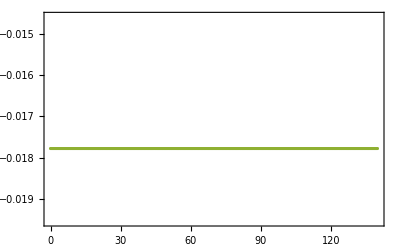

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

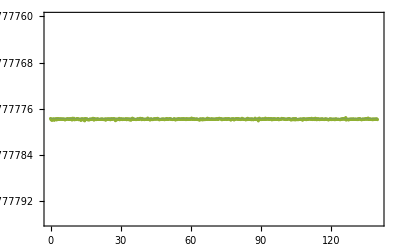

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.000001Egfmc[[1]],.999999Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-1.3510.008

```mathematica
(Egfmc-ET)/Egfmc
```

0.71.110^-8

```mathematica
2/V
```

7.5

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

1.67877

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### NLO meson

```mathematica
steps=1300;
walkers=500;
V=4/3α;
```

```mathematica
NCoord=2;
```

```mathematica
Dimensions[gfmcHammys]
```

{701,1000}

```mathematica
Dimensions[Transpose[Join[Transpose[gfmcHammys],Transpose[gfmcHammys]]]]
```

{701,2000}

```mathematica
gfmcHammys2=Transpose[Join[Transpose[gfmcHammys],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
```

```mathematica
Dimensions[gfmcWs2]
```

{1301,1500}

```mathematica
gfmcWs2=Transpose[Join[Transpose[gfmcWs],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_2.h5";
test2=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
Do[
gfmcHammys2=gfmcHammys;
gfmcWs2=gfmcWs;
dataBase=dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>".h5";
gfmcHammys=Transpose[Join[Transpose[gfmcHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcWs=Transpose[Join[Transpose[gfmcWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];
```

```mathematica
gfmcHammys[[1;;10,1;;10]]
```

{{-0.0418498,-0.0439894,-0.0372443,-0.0480988,-0.0299693,-0.0413547,-0.0404997,-0.029973,-0.0676032,-0.0324143},{-0.0413598,-0.0448293,-0.0365028,-0.0465629,-0.0298755,-0.0399963,-0.0424622,-0.0299391,-0.0660052,-0.0326782},{-0.0410898,-0.0436446,-0.0373587,-0.0488835,-0.0299085,-0.0392724,-0.0417717,-0.029668,-0.0639098,-0.0335248},{-0.0400097,-0.0431555,-0.0378482,-0.0537902,-0.0303959,-0.039711,-0.0435765,-0.0296416,-0.0609236,-0.0337464},{-0.0392411,-0.0413749,-0.0395152,-0.0546636,-0.0302452,-0.0390007,-0.0470746,-0.0300437,-0.0609198,-0.0334034},{-0.0400469,-0.041517,-0.0413222,-0.0560607,-0.0299418,-0.0396669,-0.0463775,-0.0296881,-0.056679,-0.0328406},{-0.0381377,-0.0400243,-0.0408275,-0.0572566,-0.0302252,-0.038712,-0.0457911,-0.0295647,-0.0572245,-0.0323687},{-0.0371055,-0.0394685,-0.0398213,-0.0561462,-0.0302943,-0.0383248,-0.0462469,-0.0293182,-0.0561947,-0.0324102},{-0.0362099,-0.0392585,-0.0392582,-0.0545279,-0.0302666,-0.0386001,-0.0458725,-0.0293654,-0.0564199,-0.0324041},{-0.0368379,-0.0386091,-0.0397288,-0.0515315,-0.0301191,-0.038699,-0.0442414,-0.0293483,-0.0587058,-0.0326618}}

```mathematica
test2[[1;;10,1;;10]]
```

{{-0.0418498,-0.0439894,-0.0372443,-0.0480988,-0.0299693,-0.0413547,-0.0404997,-0.029973,-0.0676032,-0.0324143},{-0.0413598,-0.0448293,-0.0365028,-0.0465629,-0.0298755,-0.0399963,-0.0424622,-0.0299391,-0.0660052,-0.0326782},{-0.0410898,-0.0436446,-0.0373587,-0.0488835,-0.0299085,-0.0392724,-0.0417717,-0.029668,-0.0639098,-0.0335248},{-0.0400097,-0.0431555,-0.0378482,-0.0537902,-0.0303959,-0.039711,-0.0435765,-0.0296416,-0.0609236,-0.0337464},{-0.0392411,-0.0413749,-0.0395152,-0.0546636,-0.0302452,-0.0390007,-0.0470746,-0.0300437,-0.0609198,-0.0334034},{-0.0400469,-0.041517,-0.0413222,-0.0560607,-0.0299418,-0.0396669,-0.0463775,-0.0296881,-0.056679,-0.0328406},{-0.0381377,-0.0400243,-0.0408275,-0.0572566,-0.0302252,-0.038712,-0.0457911,-0.0295647,-0.0572245,-0.0323687},{-0.0371055,-0.0394685,-0.0398213,-0.0561462,-0.0302943,-0.0383248,-0.0462469,-0.0293182,-0.0561947,-0.0324102},{-0.0362099,-0.0392585,-0.0392582,-0.0545279,-0.0302666,-0.0386001,-0.0458725,-0.0293654,-0.0564199,-0.0324041},{-0.0368379,-0.0386091,-0.0397288,-0.0515315,-0.0301191,-0.038699,-0.0442414,-0.0293483,-0.0587058,-0.0326618}}

```mathematica
gfmcHammys[[1;;10,501;;510]]
```

{{-0.0418498,-0.0439894,-0.0372443,-0.0480988,-0.0299693,-0.0413547,-0.0404997,-0.029973,-0.0676032,-0.0324143},{-0.0413598,-0.0448293,-0.0365028,-0.0465629,-0.0298755,-0.0399963,-0.0424622,-0.0299391,-0.0660052,-0.0326782},{-0.0410898,-0.0436446,-0.0373587,-0.0488835,-0.0299085,-0.0392724,-0.0417717,-0.029668,-0.0639098,-0.0335248},{-0.0400097,-0.0431555,-0.0378482,-0.0537902,-0.0303959,-0.039711,-0.0435765,-0.0296416,-0.0609236,-0.0337464},{-0.0392411,-0.0413749,-0.0395152,-0.0546636,-0.0302452,-0.0390007,-0.0470746,-0.0300437,-0.0609198,-0.0334034},{-0.0400469,-0.041517,-0.0413222,-0.0560607,-0.0299418,-0.0396669,-0.0463775,-0.0296881,-0.056679,-0.0328406},{-0.0381377,-0.0400243,-0.0408275,-0.0572566,-0.0302252,-0.038712,-0.0457911,-0.0295647,-0.0572245,-0.0323687},{-0.0371055,-0.0394685,-0.0398213,-0.0561462,-0.0302943,-0.0383248,-0.0462469,-0.0293182,-0.0561947,-0.0324102},{-0.0362099,-0.0392585,-0.0392582,-0.0545279,-0.0302666,-0.0386001,-0.0458725,-0.0293654,-0.0564199,-0.0324041},{-0.0368379,-0.0386091,-0.0397288,-0.0515315,-0.0301191,-0.038699,-0.0442414,-0.0293483,-0.0587058,-0.0326618}}

```mathematica
Dimensions[gfmcHammys]
```

{1301,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

1301

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{1301,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.040800.00024

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.040560.00004

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers8000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.0444370.000021

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

Import::nffil: File ~/Dropbox/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep1300_Nwalkers500_Ncoord2_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep1300_Nwalkers500_Ncoord2_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

$Failed⟦2,1⟧$Failed⟦2,2⟧

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[700]<>"_Nwalkers"<>ToString[1000]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[700]<>"_Nwalkers"<>ToString[1000]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.042590.00022

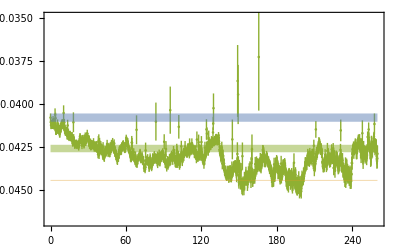

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

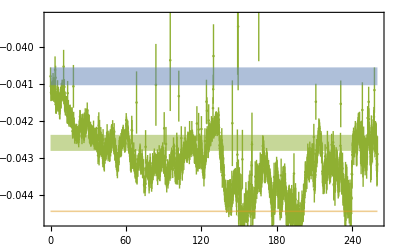

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.05Egfmc[[1]],.92Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-0.0430.005

```mathematica
(Evmc-ET)/Evmc
```

0.0820.005

```mathematica
(Egfmc-ET)/Egfmc
```

0.0420.008

```mathematica
2/V
```

7.5

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

1.67877

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### NNLO meson

```mathematica
steps=700;
walkers=1000;
V=4/3α;
```

```mathematica
NCoord=2;
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{701,1000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

701

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

1000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{701,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.06490.0005

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.040560.00004

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.06250.0012

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers8000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.069380.00013

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.069360.00032

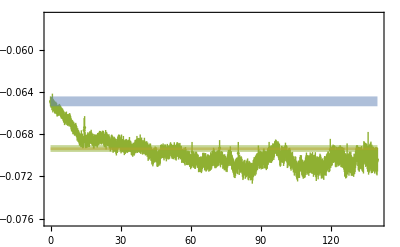

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

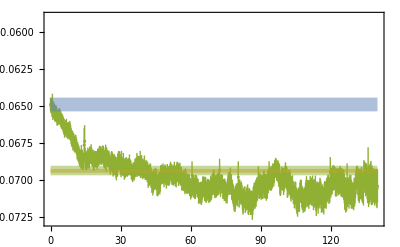

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.05Egfmc[[1]],.85Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Evmc-ET)/Evmc
```

0.0650.007

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.0000.005

```mathematica
(Egfmc-ET)/Egfmc
```

0.0640.008

```mathematica
2/V
```

7.5

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

1.67877

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### mNLO meson

```mathematica
steps=380;
walkers=2000;
V=4/3α;
```

```mathematica
NCoord=2;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{381,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

381

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{381,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.04720.0008

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.040560.00004

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_ordermNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.04390.0012

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.050770.00030

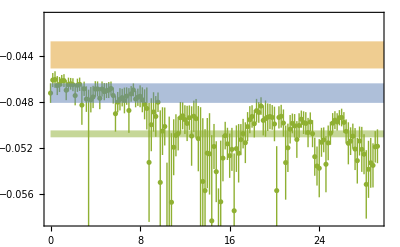

```mathematica
EMPQQbarmNLO=Show[ListPlot[{EgfmcVec[[1;;Round[Length[EgfmcVec]/2.6]]]},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.15 Egfmc[[1]],.8Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarmNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.1340.024

```mathematica
(Egfmc-ET)/Egfmc
```

0.0690.018

```mathematica
2/V
```

7.5

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

1.67877

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### LO baryon

```mathematica
steps=700;
walkers=1000;
V=4/3α/(3-1);
```

```mathematica
NCoord=3;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{701,1000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

701

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

1000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{701,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.0190630.000020

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.01014010

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.019030.00004

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.0190540.000010

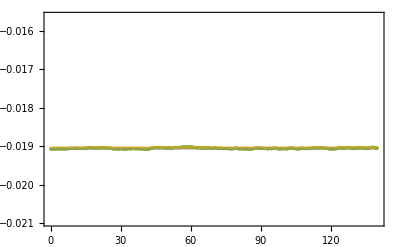

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

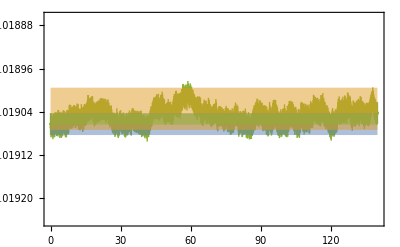

```mathematica
EMPQQQLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.01Egfmc[[1]],.99Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

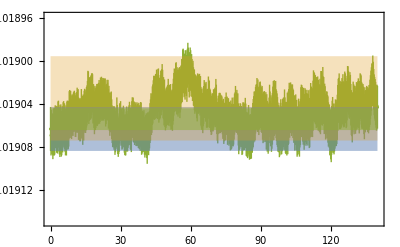

```mathematica
EMPQQQLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.005Egfmc[[1]],.995Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.3],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQQLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.00100.0021

```mathematica
(Egfmc-ET)/Egfmc
```

-0.00050.0012

```mathematica
2/V
```

15.

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

0.839387

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### NLO baryon

```mathematica
steps=700;
walkers=1000;
V=4/3α/(3-1);
```

```mathematica
NCoord=3;
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

$Aborted

```mathematica
Dimensions[gfmcHammys]
```

{701,1000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

701

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

1000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{701,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.047430.00029

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.01014010

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers8000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.049070.00016

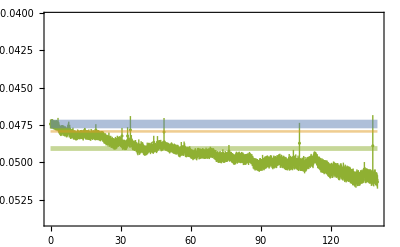

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

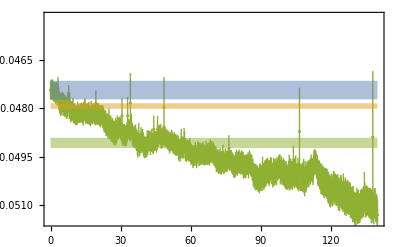

```mathematica
EMPQQQNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.05Egfmc[[1]],.92Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQQNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.0230.004

```mathematica
(Egfmc-ET)/Egfmc
```

0.0330.007

```mathematica
2/V
```

15.

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

0.839387

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### NNLO baryon

```mathematica
steps=700;
walkers=1000;
V=4/3α/(3-1);
```

```mathematica
NCoord=3;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep700_Nwalkers1000_Ncoord3_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf.h5 not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep700_Nwalkers1000_Ncoord3_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf.h5 not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
Dimensions[gfmcHammys]
```

{0}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

0

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

Part::partw: Part 2 of {0} does not exist.

{0}⟦2⟧

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

RandomInteger::array: The array dimensions {200,{0}⟦2⟧} given in position 2 of RandomInteger[{1,{0}⟦2⟧},{200,{0}⟦2⟧}] should be a list of non-negative machine-sized integers giving the dimensions for the result.

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{0}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1,2⟧

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.01014010

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.08350.0010

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep700_Nwalkers1000_Ncoord3_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep700_Nwalkers1000_Ncoord3_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

$Failed⟦2,1⟧$Failed⟦2,2⟧

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

ListPlot::prng: Value of option PlotRange -> {1.1 $Failed⟦2,1⟧,0.82 $Failed⟦2,1⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partw: Part -1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
EMPQQQNNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.05Egfmc[[1]],.85Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

ListPlot::prng: Value of option PlotRange -> {1.05 $Failed⟦2,1⟧,0.85 $Failed⟦2,1⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partw: Part -1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Export[picDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQQNNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

(0.0835236+$Failed⟦2,1⟧)/($Failed⟦2,1⟧)√(Abs[($Failed⟦2,2⟧)/($Failed⟦2,1⟧)^2]^2 (0.0835236+$Failed⟦2,1⟧)^2+(9.77022×10^-7+($Failed⟦2,2⟧)^2)/($Failed⟦2,1⟧)^2)

```mathematica
(Egfmc-ET)/Egfmc
```

(1/($Failed⟦2,1⟧)Abs[($Failed⟦2,2⟧)/($Failed⟦2,1⟧)^2]) (($Failed⟦2,1⟧$Failed⟦2,2⟧)-{}⟦1,2⟧)

```mathematica
2/V
```

15.

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

0.839387

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### mNLO baryon

```mathematica
steps=700;
walkers=1000;
V=4/3α/(3-1);
```

```mathematica
NCoord=3;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{701,1000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

701

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

1000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{701,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.05140.0005

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.01014010

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_ordermNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.05120.0010

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.055080.00027

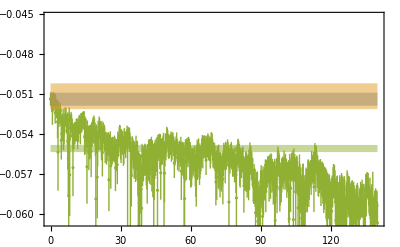

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

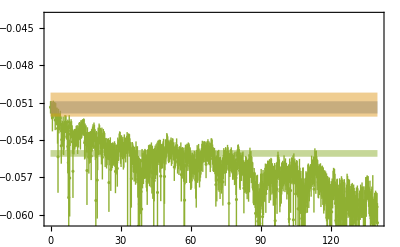

```mathematica
EMPQQQmNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1Egfmc[[1]],.8Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQQmNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.0710.018

```mathematica
(Egfmc-ET)/Egfmc
```

0.0670.010

```mathematica
2/V
```

15.

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

0.839387

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

## α=0.6

```mathematica
α=0.6;
```

```mathematica
picDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/62d1dcb0570fab737342743d/figs/";
```

### LO meson

```mathematica
steps=430;
walkers=2000;
V=4/3α;
```

```mathematica
maxStep=100;
```

```mathematica
NCoord=2;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[1;;maxStep+1,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[1;;maxStep+1,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{101,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

101

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{101,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.1600000000529

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.82120.0026

```mathematica
Egfmc=Around[-V^2/4,10^(-8)V^2/4]
```

-0.160000000016

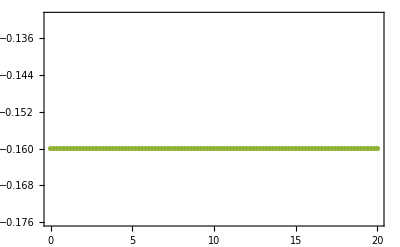

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

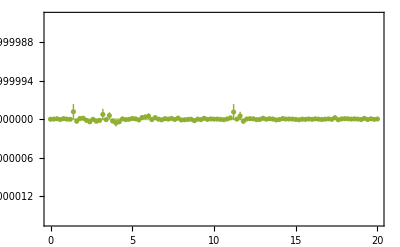

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.000001Egfmc[[1]],.999999Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-4.1330.016

```mathematica
(Egfmc-ET)/Egfmc
```

0.01.010^-8

```mathematica
2/V
```

2.5

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

5.03632

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### NLO meson

```mathematica
steps=380;
walkers=2000;
V=4/3α;
```

```mathematica
maxStep=100;
```

```mathematica
NCoord=2;
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[1;;maxStep+1,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[1;;maxStep+1,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{101,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

101

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{101,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.7810.006

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.365060.00035

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers8000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.88920.0028

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.9100.006

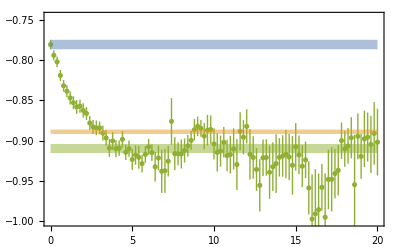

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

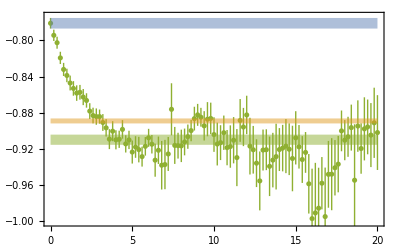

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1Egfmc[[1]],.85Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.0230.007

```mathematica
(Egfmc-ET)/Egfmc
```

0.1420.009

```mathematica
2/V
```

2.5

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

5.03632

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### NNLO meson

```mathematica
steps=393;
walkers=2000;
V=4/3α;
```

```mathematica
maxStep=50;
```

```mathematica
NCoord=2;
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[1;;maxStep+1,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[1;;maxStep+1,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{51,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

51

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{51,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-2.6990.017

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.365060.00035

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers8000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-10.200.06

```mathematica
V^2 7
```

4.48

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-3.580.07

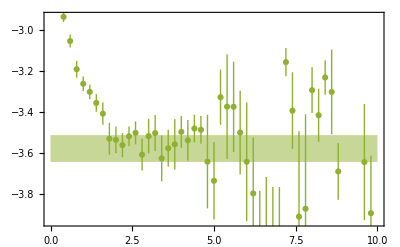

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

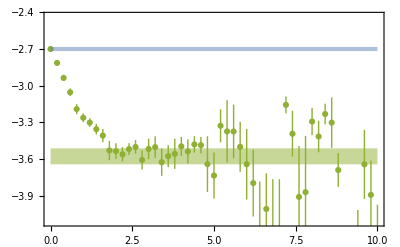

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.15Egfmc[[1]],.68Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-1.850.04

```mathematica
(Egfmc-ET)/Egfmc
```

0.2460.019

```mathematica
2/V
```

2.5

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

5.03632

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### mNLO meson

```mathematica
steps=380;
walkers=2000;
V=4/3α;
```

```mathematica
NCoord=2;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[1;;maxStep+1,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[1;;maxStep+1,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{101,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

101

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Dimensions[bootTab]
```

{101,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Indeterminate,-0.63423,-0.63423,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-6.8948,-0.63423,-0.63423,-6.90374,Indeterminate,-0.63423,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«16»,Indeterminate,Indeterminate,-0.63423,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-0.63423,-6.89942,Indeterminate,Indeterminate,-0.63423,Indeterminate,Indeterminate,Indeterminate,«150»},«19»].

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Indeterminate,-0.63423,-0.63423,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-6.8948,-0.63423,-0.63423,-6.90374,Indeterminate,-0.63423,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«16»,Indeterminate,Indeterminate,-0.63423,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-0.63423,-6.89942,Indeterminate,Indeterminate,-0.63423,Indeterminate,Indeterminate,Indeterminate,«150»},«20»].

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Indeterminate,-0.666822,-0.666822,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-3.94276,-0.666822,-0.666822,-3.9446,Indeterminate,-0.666822,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«16»,Indeterminate,Indeterminate,-0.666822,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-0.666822,-3.94371,Indeterminate,Indeterminate,-0.666822,Indeterminate,Indeterminate,Indeterminate,«150»},«19»].

General::stop: Further output of Quantile::rectn will be suppressed during this calculation.

```mathematica
ET=EgfmcVec[[1,2]]
```

-1.1530.035

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.365060.00035

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_ordermNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-1.210.12

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.70.9

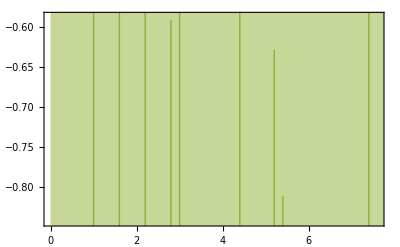

```mathematica
EMPQQbarmNLO=Show[ListPlot[{EgfmcVec[[1;;Round[Length[EgfmcVec]/2.6]]]},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.15 Egfmc[[1]],.8Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

```mathematica
Export[picDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarmNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-0.71.5

```mathematica
(Egfmc-ET)/Egfmc
```

-0.61.4

```mathematica
2/V
```

2.5

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

5.03632

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### LO baryon

```mathematica
steps=430;
walkers=2000;
V=4/3α/(3-1);
```

```mathematica
maxStep=100;
```

```mathematica
NCoord=3;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[1;;maxStep+1,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[1;;maxStep+1,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{101,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

101

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{101,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.171470.00011

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.091260.00009

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.171870.00035

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-0.171490.00005

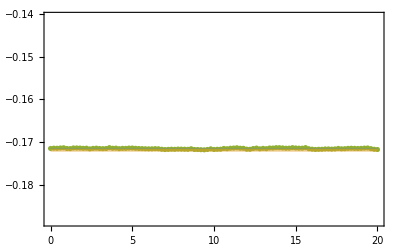

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

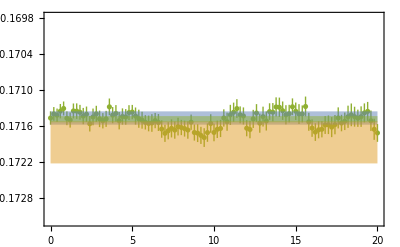

```mathematica
EMPQQQLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.01Egfmc[[1]],.99Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

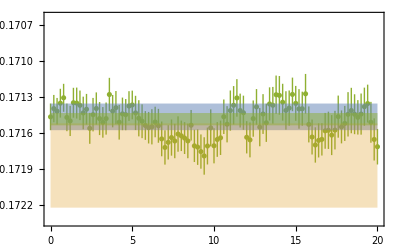

```mathematica
EMPQQQLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.005Egfmc[[1]],.995Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.3],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQQLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-0.00230.0021

```mathematica
(Egfmc-ET)/Egfmc
```

0.00010.0007

```mathematica
2/V
```

5.

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

2.51816

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### NLO baryon

```mathematica
steps=380;
walkers=2000;
V=4/3α/(3-1);
```

```mathematica
maxStep=100;
```

```mathematica
NCoord=3;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[1;;maxStep+1,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[1;;maxStep+1,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{101,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

101

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{101,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.9370.005

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.091260.00009

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-0.9160.015

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-1.1040.017

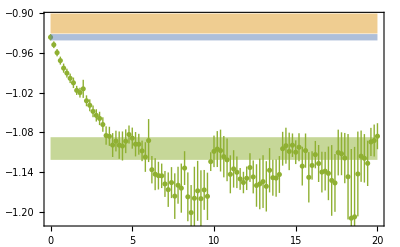

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

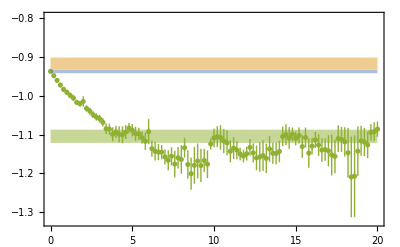

```mathematica
EMPQQQNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.2Egfmc[[1]],.72Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQQNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.1700.021

```mathematica
(Egfmc-ET)/Egfmc
```

0.1520.016

```mathematica
2/V
```

5.

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

2.51816

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### NNLO baryon

```mathematica
steps=393;
walkers=2000;
V=4/3α/(3-1);
```

```mathematica
maxStep=50;
```

```mathematica
NCoord=3;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[1;;maxStep+1,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[1;;maxStep+1,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{51,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

51

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{51,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-3.4250.018

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.091260.00009

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-3.430.06

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-4.630.05

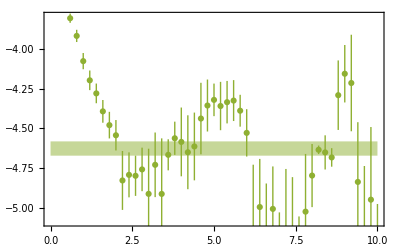

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

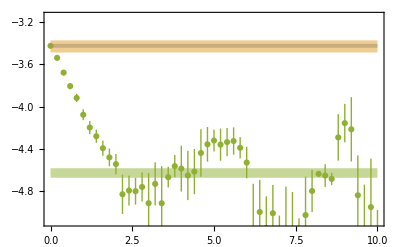

```mathematica
EMPQQQNNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1Egfmc[[1]],.68Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQQNNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.2590.016

```mathematica
(Egfmc-ET)/Egfmc
```

0.2600.011

```mathematica
2/V
```

5.

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

2.51816

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```

### mNLO baryon

```mathematica
steps=380;
walkers=2000;
V=4/3α/(3-1);
```

```mathematica
maxStep=50;
```

```mathematica
NCoord=3;
```

```mathematica
dataDir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
```

```mathematica
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[1;;maxStep+1,All,1]];
```

```mathematica
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[1;;maxStep+1,All,1]];
```

```mathematica
Dimensions[gfmcHammys]
```

{101,2000}

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

101

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

2000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
Dimensions[bootTab]
```

{101,200}

```mathematica
EgfmcVec=Table[{.2 (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-1.2340.018

```mathematica
Evmc=V^2Around[-0.5703993439674377,0.000539594329893589]
```

-0.091260.00009

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1_Ncoord"<>ToString[NCoord]<>"_cutoff1_ordermNLO_alpha"<>ToString[α]<>"_c_loss1.0_v_loss1.0.csv"]
```

-1.290.04

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,1]],Import[dataDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.csv"][[2,2]]]
```

-1.060.09

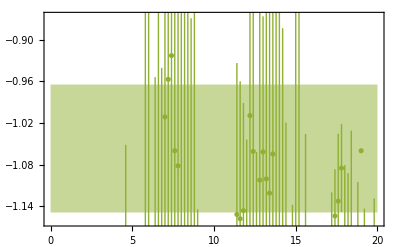

```mathematica
Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1 Egfmc[[1]],.82Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}]]
```

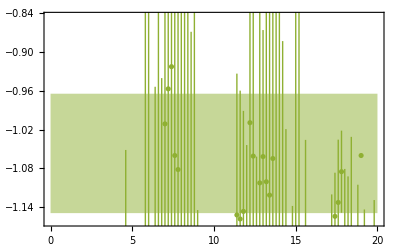

```mathematica
EMPQQQmNLO=Show[ListPlot[{EgfmcVec},PlotStyle->{ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3]},Frame->True,PlotRange->{1.1Egfmc[[1]],.8Egfmc[[1]]}],Graphics[{ColorData[97][1],Opacity[0.5],Rectangle[{0,ET[[1]]-ET[[2]]},{EgfmcVec[[-1,1]],ET[[1]]+ET[[2]]}]}],Graphics[{ColorData[97][2],Opacity[0.5],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQQmNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-0.220.10

```mathematica
(Egfmc-ET)/Egfmc
```

-0.170.09

```mathematica
2/V
```

5.

```mathematica
a=6.2954
```

6.2954

```mathematica
a V
```

2.51816

```mathematica
(*2/V-a*)
```

```mathematica
(*(2/V-a)/α*)
```

```mathematica
(*(2/V-a)α*)
```